“Title” / UD RC11 - UCL Bartlett 
1219
LIU ZIDONG

Exercise number 1

- Ex. 1: Create functions that perform the following tasks:

```mathematica
-testing if a number is even
-testing if a number is odd
-testing if a number is an integer
-testing if an element given as an argument is a list.
```

-a even if is number testing

-a if is number odd testing

-a an if integer is number testing

```mathematica
EvenQ[5]
```

False

```mathematica
OddQ[5]
```

True

```mathematica
IntegerQ[5]
```

True

```mathematica
ListQ[{5}]
```

True

```mathematica
ListQ[5]
```

False

- Ex. 2: Create functions that perform the following tasks:

```mathematica
-Adding 2 numbers (no data type)
```

-2 Adding data no numbers type

```mathematica
mySum01[a_,b_]:=a+b
```

```mathematica
mySum01[1,1]
```

2

```mathematica
-Adding 2 numbers.First number has to be an Integer, second has to be Real (it means that the data are typed).
```

```mathematica
mySum02[a_Integer,b_Real]:=a+b
```

```mathematica
mySum02[5.1,2.51]
```

mySum02[5.1,2.51]

```mathematica
mySum02[5,2.51]
```

7.51

```mathematica
-Adding an infinite amount of numbers
```

-Adding amount an infinite numbers of

```mathematica
mySum03[a_,b___]:=a+b
```

```mathematica
mySum03[1,2,3,4,5,6,8,7,9,13,5,3,51,6,8]
```

131

```mathematica
-Squaring the value of elements in a list, while checking that these elements are Integer.
```

```mathematica
Function04[mylist_/;IntegerQ/@mylist]:=mylist^2
```

```mathematica
Function04[{1,2,3,4}]
```

{1,4,9,16}

```mathematica
Function04[{13.2,5,3,8}]
```

Function04[{13.2,5,3,8}]

```mathematica
-Computing the square root of a number, while making sure that you do that only if the sum of all the numbers is superior or equal to 100.
```

I don’t know why it doesn’t work

```mathematica
Function05[a_/;And@@(Total[a]≥100)]:=Sqrt[a]
```

```mathematica
Function05[{1,4}]
```

{1,2}

```mathematica
Computing the sum of a series of number,while making sure,firstly that each number is even,that each number can be divided by 5,and that the total amount of number is at least 10. (it means that if I consider the list of numbers as a Set,the Cardinal of the set has to be>or equal to 10.
```

```mathematica
I don't know why Function06 and Function07 don't work neither.I can't understand the difference between "And@@" and "&&". 
Is "And@@"  necessary?
I don't know why Function 08 works. I just change the order of condition.
```

```mathematica
Function06[a_/;EvenQ/@a&&IntegerQ/@(a/5)&&Length[a]≥10]:=Total[a]
```

```mathematica
Function06[{10,40}]
```

Function06[{10,40}]

```mathematica
Function06[{10,20,30,40,50,60,70,80,90,100}]
```

{10,20,30,40,50,60,70,80,90,100}

```mathematica
Function07[a_/;And@@(EvenQ/@a)&&And@@(IntegerQ/@(a/5))&&And@@Length[a]≥10]:=Total[a]
```

```mathematica
Function07[{10,40}]
```

50

```mathematica
Function07[{10,20,30,40,50,60,70,80,90,100,110}]
```

660

```mathematica
Function08[a_/;And@@(IntegerQ/@(a/5))&&And@@(EvenQ/@a)&&And@@Length[a]≥10]:=Total[a]
```

```mathematica
Function08[{11,20,30,40,50,60,70,80,90,100,110}]
```

Function08[{11,20,30,40,50,60,70,80,90,100,110}]

-Ex.3:Create functions that perform the following tasks:

```mathematica
-Write a function that compute the factorial of a list.Firstly,use the built-in Mathematica function,secondly,write a recursive function.
```

```mathematica
f[0]=1
f[1]=1
f[n_]:=f[n-1]*n
```

1

1

```mathematica
?f
```

```mathematica
f[2]
```

2

```mathematica
f[3]
```

6

```mathematica
-Write a function that associate a letter to the result of the factorial in this way.Letter "a" should be associated to the result of Factorial[1],"b" to Factorial[2],etc.
```

```mathematica
<|a->f[1],b->f[2]|>
```

<|a→1,b→2|>

```mathematica
-Write a function that is computing the difference of two successive values in a list with at least 10 elements.
```

```mathematica
d[a_/;And@@(Length[a]≥10)]:=Differences[a]
```

```mathematica
d[{1,3,5,8,2,6,9,1,35,5,8}]
```

{2,2,3,-6,4,3,-8,34,-30,3}

```mathematica
-Write a function that associate a Point to each value given by the previous function.The diameter of the Point should be given by the "difference" values.
```

Sorry, I don’t know whether I understand the question...

```mathematica
K[n_]:=Differences[{1,6,7,3,5,9,15,6,2,12,13},n]
```

```mathematica
Table[K[x],{x,1,5}]
```

{{5,1,-4,2,4,6,-9,-4,10,1},{-4,-5,6,2,2,-15,5,14,-9},{-1,11,-4,0,-17,20,9,-23},{12,-15,4,-17,37,-11,-32},{-27,19,-21,54,-48,-21}}

```mathematica
G[x_]:=Abs[Total[K[x]]]
```

```mathematica
Table[G[x],{x,1,5}]
```

{12,4,5,22,44}

```mathematica
Table[{PointSize[G[t]],Point[{t,t}]},{t,1,5}]
```

{{PointSize[12],Point[{1,1}]},{PointSize[4],Point[{2,2}]},{PointSize[5],Point[{3,3}]},{PointSize[22],Point[{4,4}]},{PointSize[44],Point[{5,5}]}}

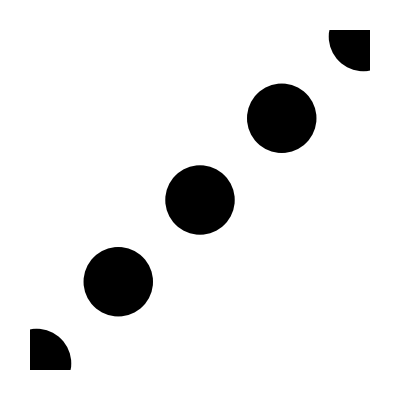

```mathematica
Graphics[Table[{PointSize[G[t]],Point[{t,t}]},{t,1,5}]]
```

```mathematica
-Write a function that create a segment (a Line) joining each successive value,and that put the center of the points at the centres of each segment.
```

```mathematica
Sorry, because I can't understand the  former question, I don't know how to go further...
```

{{1,3},{1,2},{3,2},{3,4},{5,2},{4,2},{3,1}}

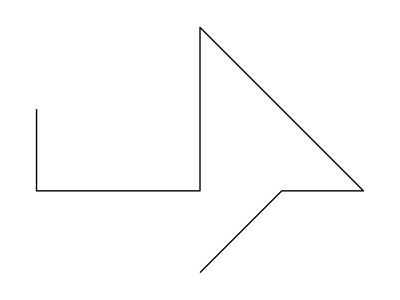

```mathematica
mylist={{1,3},{1,2},{3,2},{3,4},{5,2},{4,2},{3,1}}
Graphics[Line[mylist]]
```

```mathematica
-Make this function dynamic by using manipulate (change the diameter of the Points (I mean the circle),change the positions of the points (I mean the input values).
```